# Versuch 49

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15]}
```

{Frame→True,Axes→False,FrameStyle→Directive[GrayLevel[0],Thickness[0.003]],ImageSize→700,FrameTicksStyle→Directive[GrayLevel[0],15]}

## Data

```mathematica
(*rawData=Import[NotebookDirectory[]<>"Messung Franck-Hertz-Kurve für Neon 1.txt"];*)
```

```mathematica
rawData=Import[NotebookDirectory[]<>"Messung Franck-Hertz-Kurve für Quecksilber 2.txt"];
```

```mathematica
data=Map[StringReplace[","->"."],StringSplit[StringSplit[rawData,"\n"],"	"]][[2;;]];
```

```mathematica
data=Map[ToExpression,data,{2}];
```

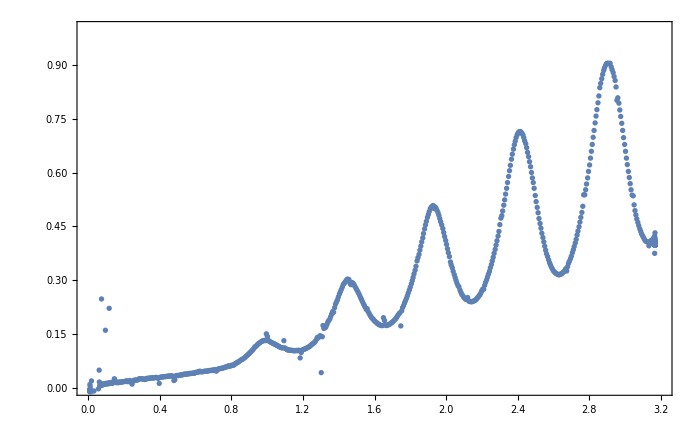

```mathematica
ListPlot[data[[All,{2,3}]],PlotRange->{{0,3.2},{0,1}},pltsettings]
```